```mathematica
ClearAll[J,L, H, v1,v2,p1,p2,m1,m2,l1,l2,θ1,θ2,ω1,ω2,x1,x2,y1,y2,α, θ, Ω1, Ω2]
```

```mathematica
l1 = l2 = m1 = m2 = 1;
g=0;
```

```mathematica
x1 = l1 Sin[θ[t]];
y1 = l1 Cos[θ[t]];
x2 = x1 + l2 Sin[α[t]+θ[t]];
y2 = y1 + l2 Cos[α[t]+θ[t]];
```

```mathematica
L = (1/2)( m1(D[x1,t]^2 +D[y1,t]^2) + m2(D[x2,t]^2 +D[y2,t]^2)) - m1 g y1 - m2 g y2//FullSimplify ;
L = FullSimplify[L/.{θ'[t]->ω1,α'[t]->ω2, θ[t]->θ, α[t]->α}];
e =FullSimplify[ D[L,ω1]ω1 + D[L,ω2]ω2 - L];
Print["L = ", L];
Print["E = ", e];
```

L = 1/2 (3 ω1^2+2 ω1 ω2+ω2^2+2 ω1 (ω1+ω2) Cos[α])

E = 1/2 (3 ω1^2+2 ω1 ω2+ω2^2)+ω1 (ω1+ω2) Cos[α]

```mathematica
Collect[L, {ω1, ω2}]
```

ω2^2/2+1/2 ω1 ω2 (2+2 Cos[α])+1/2 ω1^2 (3+2 Cos[α])

```mathematica
Llin = 1/2 ω1 ω2 (2+2 Cos[α]);
A = Llin/.{ α->α[t],ω2->α'[t], ω1->θ'[t]};
D[D[A, θ'[t]],t]//FullSimplify
D[D[A, α'[t]],t]-D[A,α[t]]//FullSimplify
```

-Sin[α[t]] α'[t]^2+(1+Cos[α[t]]) α''[t]

(1+Cos[α[t]]) θ''[t]

```mathematica
M = ({{3+2Cos[α], (1+Cos[α])}, {(1+Cos[α]), 1}});
 L ==(1/2){ ω1, ω2}.M. {ω1, ω2}//FullSimplify
```

True

```mathematica
μrule = Solve[μ == D[L, ω1],ω1] ;
L/.μrule//FullSimplify//First
R =( L - μ ω1)/.μrule//FullSimplify//First
```

(μ^2+2 ω2^2-ω2^2 Cos[α]^2)/(6+4 Cos[α])

(-μ^2+2 μ ω2+2 ω2^2+ω2 Cos[α] (2 μ-ω2 Cos[α]))/(6+4 Cos[α])

```mathematica
Collect[%, ω2]
```

-μ^2/(6+4 Cos[α])+(ω2 (2 μ+2 μ Cos[α]))/(6+4 Cos[α])+(ω2^2 (2-Cos[α]^2))/(6+4 Cos[α])

```mathematica
Veff = μ^2/(6+4 Cos[α]);
Rlin = (ω2 μ(1+ Cos[α]))/(3+2 Cos[α]);
Rkinetic = (ω2^2 (1+Sin[α]^2))/(6+4 Cos[α]);
Rkinetic + Rlin - Veff == R//FullSimplify
```

True

```mathematica
A = Rlin/.{ α->α[t],ω2->α'[t]};
D[D[A, α'[t]],t]-D[A,α[t]]//FullSimplify
```

0

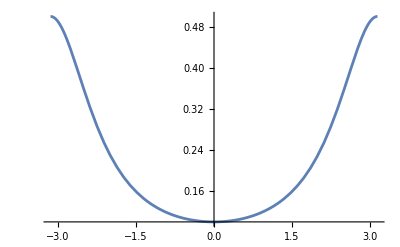

```mathematica
Plot[Veff/.{μ->1},{α,-Pi,Pi}]
```

```mathematica
$Assumptions = 0 <= α < 2Pi;
Solve[D[Veff, α]==0, α]
D[Veff, {α,2}]/.%
```

{{α→0},{α→π}}

{μ^2/25,-μ^2}

```mathematica
Hred = ( p ω2 - R)/.Solve[p == D[R, ω2], ω2]//FullSimplify//First
```

-(3 p^2-2 p μ+μ^2+2 p (p-μ) Cos[α])/(-3+Cos[2 α])

```mathematica
{Ω1, Ω2} ={ω1, ω2}/.Flatten[ Solve[ p1 == D[L, ω1] && p2 == D[L, ω2], {ω1,ω2}]];
H = Collect[Expand[Simplify[{p1, p2}.{Ω1,Ω2} - L/.{ω1->Ω1,ω2->Ω2}]], {p1,p2}]//FullSimplify
```

(-p1^2+2 p1 p2-3 p2^2+2 (p1-p2) p2 Cos[α])/(-3+Cos[2 α])

```mathematica
(H/.{p1->μ, p2->p})==Hred //FullSimplify
```

True